```mathematica
<<PlotLegends`
```

```mathematica
grumixama120131203=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\grumixama\\1_20131203.xlsx"];
grumixama220131203=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\grumixama\\2_20131203.xlsx"];
grumixama320131203=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\grumixama\\3_20131203.xlsx"];
grumixama420131203=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\grumixama\\4_20131203.xlsx"];
grumixama520131203=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\grumixama\\5_20131203.xlsx"];
```

```mathematica
tempo=Table[grumixama120131203[[1,i,1]],{i,1,Length[grumixama120131203[[1]]]}];
```

```mathematica
transp120131203=Table[grumixama120131203[[1,i,2]],{i,1,Length[tempo]}];
transp220131203=Table[grumixama220131203[[1,i,2]],{i,1,Length[tempo]}];
transp320131203=Table[grumixama320131203[[1,i,2]],{i,1,Length[tempo]}];
transp420131203=Table[grumixama420131203[[1,i,2]],{i,1,Length[tempo]}];
transp520131203=Table[grumixama520131203[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120131203=Table[grumixama120131203[[1,i,3]],{i,1,Length[tempo]}];
par220131203=Table[grumixama220131203[[1,i,3]],{i,1,Length[tempo]}];
par320131203=Table[grumixama320131203[[1,i,3]],{i,1,Length[tempo]}];
par420131203=Table[grumixama420131203[[1,i,3]],{i,1,Length[tempo]}];
par520131203=Table[grumixama520131203[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120131203=Table[grumixama120131203[[1,i,4]],{i,1,Length[tempo]}];
dpv220131203=Table[grumixama220131203[[1,i,4]],{i,1,Length[tempo]}];
dpv320131203=Table[grumixama320131203[[1,i,4]],{i,1,Length[tempo]}];
dpv420131203=Table[grumixama420131203[[1,i,4]],{i,1,Length[tempo]}];
dpv420131203=Table[grumixama420131203[[1,i,4]],{i,1,Length[tempo]}];
dpv520131203=Table[grumixama520131203[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120131203=N[Table[{tempo[[i]],transp120131203[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220131203=N[Table[{tempo[[i]],transp220131203[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320131203=N[Table[{tempo[[i]],transp320131203[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420131203=N[Table[{tempo[[i]],transp420131203[[i]]},{i,1,Length[tempo]}]];
transpVsTempo520131203=N[Table[{tempo[[i]],transp520131203[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120131203=N[Table[{tempo[[i]],par120131203[[i]]},{i,1,Length[tempo]}]];
parVsTempo220131203=N[Table[{tempo[[i]],par220131203[[i]]},{i,1,Length[tempo]}]];
parVsTempo320131203=N[Table[{tempo[[i]],par320131203[[i]]},{i,1,Length[tempo]}]];
parVsTempo420131203=N[Table[{tempo[[i]],par420131203[[i]]},{i,1,Length[tempo]}]];
parVsTempo520131203=N[Table[{tempo[[i]],par520131203[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120131203=N[Table[{tempo[[i]],dpv120131203[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220131203=N[Table[{tempo[[i]],dpv220131203[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320131203=N[Table[{tempo[[i]],dpv320131203[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420131203=N[Table[{tempo[[i]],dpv420131203[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo520131203=N[Table[{tempo[[i]],dpv520131203[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120131203=Table[transp120131203[[i]]/par120131203[[i]],{i,2,Length[tempo]}];
transpSobrePAR220131203=Table[transp220131203[[i]]/par220131203[[i]],{i,2,Length[tempo]}];
transpSobrePAR320131203=Table[transp320131203[[i]]/par320131203[[i]],{i,2,Length[tempo]}];transpSobrePAR420131203=Table[transp420131203[[i]]/par420131203[[i]],{i,2,Length[tempo]}];
transpSobrePAR520131203=Table[transp520131203[[i]]/par520131203[[i]],{i,2,Length[tempo]}];
```

```mathematica
transpSobrePARVsTempo120131203=N[Table[{tempo[[i]],transpSobrePAR120131203[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220131203=N[Table[{tempo[[i]],transpSobrePAR220131203[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320131203=N[Table[{tempo[[i]],transpSobrePAR320131203[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420131203=N[Table[{tempo[[i]],transpSobrePAR420131203[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo520131203=N[Table[{tempo[[i]],transpSobrePAR520131203[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120131203=Table[transp120131203[[i]]/dpv120131203[[i]],{i,1,Length[tempo]}];
transpSobreDPV220131203=Table[transp220131203[[i]]/dpv220131203[[i]],{i,1,Length[tempo]}];
transpSobreDPV320131203=Table[transp320131203[[i]]/dpv320131203[[i]],{i,1,Length[tempo]}];transpSobreDPV420131203=Table[transp420131203[[i]]/dpv420131203[[i]],{i,1,Length[tempo]}];
transpSobreDPV520131203=Table[transp520131203[[i]]/dpv520131203[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120131203=N[Table[{tempo[[i]],transpSobreDPV120131203[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220131203=N[Table[{tempo[[i]],transpSobreDPV220131203[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320131203=N[Table[{tempo[[i]],transpSobreDPV320131203[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420131203=N[Table[{tempo[[i]],transpSobreDPV420131203[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo520131203=N[Table[{tempo[[i]],transpSobreDPV520131203[[i]]},{i,1,Length[tempo]}]];
```

## Grumixama - 03/12/2013 - Transpiração

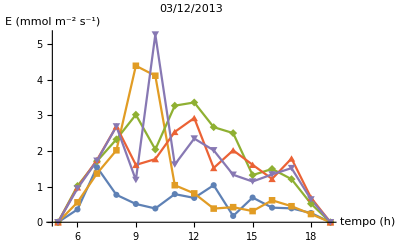

```mathematica
g1=ListLinePlot[{transpVsTempo120131203,transpVsTempo220131203,transpVsTempo320131203,transpVsTempo420131203,transpVsTempo520131203},PlotLegend->{"-0.92MPa","-0.78MPa","-0.35MPa","-0.39MPa","-0.36MPa"},LegendPosition->{.7,-0.4},PlotLabel->"03/12/2013",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Grumixama - 03/12/2013 - PAR ( radiação fotossinteticamente ativa)

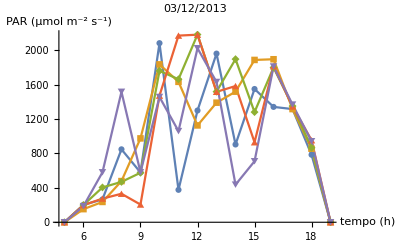

```mathematica
g2=ListLinePlot[{parVsTempo120131203,parVsTempo220131203,parVsTempo320131203,parVsTempo420131203,parVsTempo520131203},PlotLegend->{"-0.92MPa","-0.78MPa","-0.35MPa","-0.39MPa","-0.36MPa"},LegendPosition->{.7,-0.4},PlotLabel->"03/12/2013",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Grumixama - 03/12/2013 - DPV (déficit de pressão de vapor)

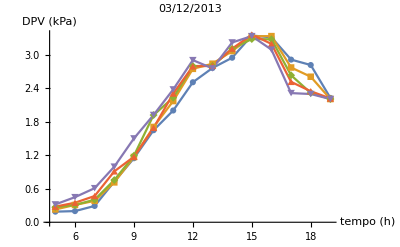

```mathematica
g3=ListLinePlot[{dpvVsTempo120131203,dpvVsTempo220131203,dpvVsTempo320131203,dpvVsTempo420131203,dpvVsTempo520131203},PlotLegend->{"-0.92MPa","-0.78MPa","-0.35MPa","-0.39MPa","-0.36MPa"},LegendPosition->{.7,-0.4},PlotLabel->"03/12/2013",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Grumixama - 03/12/2013 - Relação Transpiração - PAR

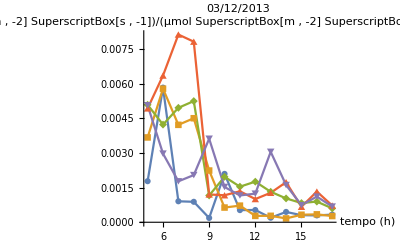

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120131203,transpSobrePARVsTempo220131203,transpSobrePARVsTempo320131203,transpSobrePARVsTempo420131203,transpSobrePARVsTempo520131203},PlotLegend->{"-0.92MPa","-0.78MPa","-0.35MPa","-0.39MPa","-0.36MPa"},LegendPosition->{.7,-0.4},PlotLabel->"03/12/2013",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Grumixama - 03/12/2013 - Relação Transpiração - DPV

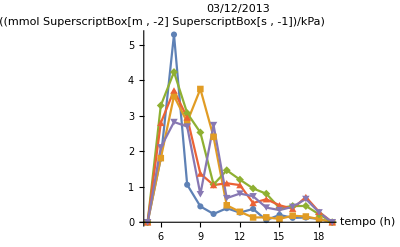

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120131203,transpSobreDPVVsTempo220131203,transpSobreDPVVsTempo320131203,transpSobreDPVVsTempo420131203,transpSobreDPVVsTempo520131203},PlotLegend->{"-0.92MPa","-0.78MPa","-0.35MPa","-0.39MPa","-0.36MPa"},LegendPosition->{.7,-0.4},PlotLabel->"03/12/2013",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```